## Funkcije

```mathematica
Funkcije geometrije
```

Funkcije geometrije

```mathematica
(* Računanje števila in dimenzije segmentov v strukturi *)
izracunajSegmenteSirine[s_,d_,n_]:=Module[
{hPrib, nPrib,nS, hS},
(* Iskanje ustrezne širine in število segmentov *)
hPrib = (4 s + 2 d)/n; (* Prib. dolžina segmenta *)
nPrib = s/hPrib;  (* Prib. št. segmentov na polovici širine *)
nS = Round[nPrib]; (* Točno št. segmentov na pol. šir. *)
hS = s/nS; (* Točna, ustrezna dolžina segmenta širine *)
Return[{hS, nS}] (* Vrne seznam {dolžina segmenta širine, število segmentov na polovici širine} *)
]

izracunajSegmenteDebeline[s_,d_,n_]:=Module[
{hPrib, nPrib,nD, hD},
hPrib= (4 s + 2 d)/n; (* Približna dolžina segmenta *)
nPrib = d/hPrib; (* Približno število segmentov na eni debelini *)
nD = Round[nPrib]; (* Točno število segmentov na eni debelini *)
hD = d/nD;  (* Točna, ustrezna dolžina segmenta debeline *)
Return[{hD, nD}] (* Vrne seznam {dolžina segmenta debeline, število segmentov na debelini} *)
]

(* Risanje točk v strukturi *)
izracunajTockePravokotnika[s_,d_,n_, H0_, brezVrha_, brezDna_, izbrisaneTockeVrha_]:=Module[
{hS,hD,nS,nD,xKoord, yKoord, i, tockeStrukture, stSegKoncno, nZaZbrisat, zacetekBrisanja, vektDolzSegm},   (* Seznam lokalnih spremenljivk v tem modulu *)
(* Pomen argumentov:;
s -> polovica širine objekta;
d -> debelina objekta;
n -> približno število segmentov na strukturi;
H0 -> offset strukture po Y osi;
brezVrha -> Če je true, izpusti točke zgornje stranice pravokotnika;
brezDna -> Če je true, izpusti točke spodnje stranice pravokotnika;
izbrisaneTockeVrha -> Če ni 0, naj izbriše točke na vrhu, ki so od simetrale oddaljene manj ali za to dolžino. 
Glej *** na skici. To se uporablja za izpuščanje točk na substratu, za pripravo meje substr.-prevodnik. *)

(* Izračun sledečih podatkov:;
hS -> dolžina segmenta širine;
hD -> dolžina segmenta debeline;
nS -> št. segmentov po polovici širine;
nD -> št. segmentov po debelini;
*)

(* SKICA:
       3;
  ----***|***----
|                |
| 4              | 2
|                |
 -------|-------;
      5         1
*)
{hS, nS}=izracunajSegmenteSirine[s,d,n];
{hD, nD}=izracunajSegmenteDebeline[s,d,n];

(* izračun točk *)
Switch[{brezVrha, brezDna}, 
{False, False}, (* Z VRHOM IN DNOM *)
(* izračun X koordinat *)
xKoord=Table[i*hS-hS/2, {i,1,nS}]; (* 1  *)
xKoord=Join[xKoord,Table[s, {i,1,nD}]]; (* 2  *)
xKoord=Join[xKoord,Table[s-i hS+hS/2, {i,1,2 nS}]]; (* 3  *)
xKoord=Join[xKoord,Table[-s, {i,1,nD}]]; (* 4 *)
xKoord=Join[xKoord,Table[-s+i hS-hS/2, {i,1,nS}]]; (* 5 *)
(* izračun Y koordinat *)
yKoord=Table[H0, {i,1,nS}]; (* 1  *)
yKoord=Join[yKoord,Table[H0+i hD-hD/2, {i,1,nD}]]; (* 2  *)
yKoord=Join[yKoord,Table[H0+d, {i,1,2 nS}]]; (* 3  *)
yKoord=Join[yKoord,Table[H0+d-i hD+hD/2, {i,1,nD}]]; (* 4 *)
yKoord=Join[yKoord,Table[H0, {i,1,nS}]], (* 5 *)
{False, True}, (* BREZ DNA *)
(* izračun X koordinat *)
xKoord=Table[s, {i,1,nD}]; (* 2  *)
xKoord=Join[xKoord,Table[s-i hS+hS/2, {i,1,2 nS}]]; (* 3  *)
xKoord=Join[xKoord,Table[-s, {i,1,nD}]]; (* 4 *)
(* izračun Y koordinat *)
yKoord=Table[H0+i hD-hD/2, {i,1,nD}]; (* 2  *)
yKoord=Join[yKoord,Table[H0+d, {i,1,2 nS}]]; (* 3  *)
yKoord=Join[yKoord,Table[H0+d-i hD+hD/2, {i,1,nD}]],(* 4 *)
{True, False}, (* BREZ VRHA *)
(* izračun X koordinat *)
xKoord=Table[i*hS-hS/2, {i,1,nS}]; (* 1  *)
xKoord=Join[xKoord,Table[s, {i,1,nD}]]; (* 2  *)
xKoord=Join[xKoord,Table[-s, {i,1,nD}]]; (* 4 *)
xKoord=Join[xKoord,Table[-s+i hS-hS/2, {i,1,nS}]]; (* 5 *)
(* izračun Y koordinat *)
yKoord=Table[H0, {i,1,nS}]; (* 1  *)
yKoord=Join[yKoord,Table[H0+i hD-hD/2, {i,1,nD}]]; (* 2  *)
yKoord=Join[yKoord,Table[H0+d-i hD+hD/2, {i,1,nD}]]; (* 4 *)
yKoord=Join[yKoord,Table[H0, {i,1,nS}]],(* 5 *)
{True, True}, (* BREZ VRHA IN DNA *)
(* izračun X koordinat *)
xKoord=Table[s, {i,1,nD}]; (* 2  *)
xKoord=Join[xKoord,Table[-s, {i,1,nD}]]; (* 4 *)
(* izračun Y koordinat *)
yKoord=Table[H0+i hD-hD/2, {i,1,nD}]; (* 2  *)
yKoord=Join[yKoord,Table[H0+d-i hD+hD/2, {i,1,nD}]];(* 4 *)
]
(* Sestavi obe koordinati *);
tockeStrukture=Table[{xKoord[[i]],yKoord[[i]]}, {i,1, Length[xKoord]}];

(* Brisanje segmentov vrha *)
If[izbrisaneTockeVrha!=0,
nZaZbrisat = Round[izbrisaneTockeVrha/hS]; (*Število točk za zbrisat v eno smer*)
zacetekBrisanja=Length[tockeStrukture]/2-nZaZbrisat+1;
tockeStrukture=Delete[tockeStrukture, Table[{i},{i, zacetekBrisanja, zacetekBrisanja+2 nZaZbrisat-1}]];
];

(* Izračunaj število segmentov *)
stSegKoncno = Length[tockeStrukture]; 

(*Sestavljanje vektorja dolžin segmentov*)
Switch[{brezVrha, brezDna}, 
{False, False}, (* Z VRHOM IN DNOM *)
vektDolzSegm=Table[hS, {i,1,nS}]; (* 1  *)
vektDolzSegm=Join[vektDolzSegm,Table[hD, {i,1,nD}]]; (* 2  *)
vektDolzSegm=Join[vektDolzSegm,Table[hS, {i,1,2 nS}]]; (* 3  *)
vektDolzSegm=Join[vektDolzSegm,Table[hD, {i,1,nD}]]; (* 4 *)
vektDolzSegm=Join[vektDolzSegm,Table[hS, {i,1,nS}]], (* 5 *)
{False, True}, (* BREZ DNA *)
vektDolzSegm=Table[hD, {i,1,nD}]; (* 2  *)
vektDolzSegm=Join[vektDolzSegm,Table[hS, {i,1,2 nS}]]; (* 3  *)
vektDolzSegm=Join[vektDolzSegm,Table[hD, {i,1,nD}]], (* 4 *)
{True, False}, (* BREZ VRHA *)
vektDolzSegm=Table[hS, {i,1,nS}]; (* 1  *)
vektDolzSegm=Join[vektDolzSegm,Table[hD, {i,1,nD}]]; (* 2  *)
vektDolzSegm=Join[vektDolzSegm,Table[hD, {i,1,nD}]]; (* 4 *)
vektDolzSegm=Join[vektDolzSegm,Table[hS, {i,1,nS}]], (* 5 *)
{True, True}, (* BREZ VRHA IN DNA *)
vektDolzSegm=Table[hD, {i,1,nD}]; (* 2  *)
vektDolzSegm=Join[vektDolzSegm,Table[hD, {i,1,nD}]](* 4 *)
];
(*Brisanje segmentov širine*)
If[izbrisaneTockeVrha!=0,
nZaZbrisat = Round[izbrisaneTockeVrha/hS]; 
zacetekBrisanja=Length[vektDolzSegm]/2-nZaZbrisat+1;
vektDolzSegm=Delete[vektDolzSegm, Table[{i},{i, zacetekBrisanja, zacetekBrisanja+2 nZaZbrisat-1}]];
];

Return[{tockeStrukture,vektDolzSegm, stSegKoncno}]
];

vrniVektorRazdalje[{xi_, yi_}, {xj_, yj_}]:=Module[
{},
Return[{(xj-xi),(yj-yi)}]
];

vrniZrcaljenVektorRazdalje[{xi_, yi_}, {xj_, yj_}]:=Module[
{},
Return[{(xj-xi),(yj+yi)}]
];


vrniKoteNormalSegmentov[obj_]:=Module[
{a, b, v, fiTan, fiNorm, fiArr,i},
(*Gre čez točke objekta, na podlagi sosednjih točk izračuna ;
kot normalnega vektorja glede na x os grafa. Ker predvidevamo ostre;
robove objektov, na koncu gre čez kote in popravi zaobljene robove.;
Za argument prejme matriko točk objekta {{x1,y1},{x2,y2},..};
Vrne matriko kotov normal v vseh središčih segmentov.*)
fiArr=Table[0, {i,1,Length[obj]}];

For[i=1, i<=(Length[obj]), i++,
Which[i==1,a=obj[[2]]; b=obj[[3]], (*Če je to 1. segment, naj raje vzame naslednji dve točki, ker segment 0 ne obstaja*)
i==Length[obj],a=obj[[i-2]]; b=obj[[i-1]], (*Če je to zadnji segment, naj raje vzame predzadnja dva, ne pa i+1 segment*)
True, a=obj[[i-1]]; b=obj[[i+1]]; (*Else, za vse običajne primere*)
];
v=vrniVektorRazdalje[a,b]; (*Vrne vektor od a do b*)
fiTan=ArcTan[v[[1]], v[[2]]];
fiNorm = Mod[(fiTan-Pi/2), (2 Pi)];
fiArr[[i]]=fiNorm;
];
(*Popravljanje zaobljenih robov*)
For[i=2, i<=(Length[fiArr]-2), i++,
If[fiArr[[i-1]]!=fiArr[[i]] && fiArr[[i]]!=fiArr[[i+1]]&&fiArr[[i+1]]!=fiArr[[i+2]], (*Če so štirje koti zaporedoma različni, je to koleno *)
fiArr[[i]]=fiArr[[i-1]]; fiArr[[i+1]]=fiArr[[i+2]]; (*Popravi nepravilna kota v kolenu na sosednje vrednosti*)
];
];

Return[fiArr];
];


vrniNormalneVektorjeSegmentovVTočki[obj_]:=Module[
(* Vrne seznam enotskih normalnih vektorjev za posamezne segmente objekta V TOČKI
VRAČA OBLIKO {{x0,y0},{x1,y1}} *)
{vectArr, angleArr,centerPoint, vectorEnd, currentVector,i },
angleArr=vrniKoteNormalSegmentov[obj];
vectArr = Table[0, {i,1, Length[obj]}];
For[i=1, i<=Length[obj], i++,
centerPoint=obj[[i]];(*rep vektorja*)
vectorEnd={centerPoint[[1]]+1 Cos[angleArr[[i]]], centerPoint[[2]]+1 Sin[angleArr[[i]]] };(*Glava vektorja*)
currentVector = {centerPoint, vectorEnd}; (*Končni vektor normale iz središča segmenta*)
(*Print["Norma normalnega vektorja ",currentVector, " je ", ((Sqrt[(vectorEnd[[2]]-centerPoint[[2]])^2+(vectorEnd[[1]]-centerPoint[[1]])^2])//N)];*)
vectArr[[i]]=currentVector;
];
Return[vectArr];
];

vrniNormalneVektorjeSegmentov[obj_]:=Module[
(*Popravek na zgoraj, vrača le vektor, obliko {x,y}*)
{vektorji},
vektorji=vrniNormalneVektorjeSegmentovVTočki[obj]; 
For[i = 1, i<=Length[vektorji],i++,
vektorji[[i]]=vrniVektorRazdalje[vektorji[[i]][[1]], vektorji[[i]][[2]]]];
Return[vektorji];
];
```

```mathematica
Funkcije za generiranje matrik
```

Funkcije generiranje matrik za

#### Pripravi sezname podatkov

```mathematica
združiVektorja[a_, b_]:=Module[{},Return[Join[a,b]]];
(* Združi vektorja. Primer. A = tocke prevodnika, B = tocke substrata.
Returna združeno {A,B}. *)

izračunajBjk[Tk_, Tj_, lk_]:=Module[{},
(* Izračuna b_jk v zgornji polovici matrike A -> razdalje v enačbi prevodnika*)
(* Funkcija sama handla tudi primer j=k *)
If[Tk==Tj,
(*j=k*) Return[1/(lk/(2 E))], 
(*j!=k*) Return[Norm[vrniZrcaljenVektorRazdalje[Tk, Tj]]/Norm[vrniVektorRazdalje[Tk, Tj]]];];];


izračunajAk[Tk_, lk_, nk_, beta_]:=Module[{vektor, dkk},
(* Izračuna a_k v spodnji polovici matrike A -> lastni prispevek dielektrika*)
vektor = vrniZrcaljenVektorRazdalje[Tk, Tk];
dkk =-vektor/Dot[vektor, vektor];
Return[1/lk - beta/Pi Dot[dkk, nk]];];


izračunajDjk[Tk_, Tj_]:=Module[
(* Izračuna d_jk v spodnji polovici matrike A -> razdalje pr dielektriku*)
{Pjk, Pzjk},
Pjk=vrniVektorRazdalje[Tj,Tk];
Pzjk=vrniZrcaljenVektorRazdalje[Tj, Tk];
Return[Pjk/Dot[Pjk, Pjk]-Pzjk/Dot[Pzjk, Pzjk]];];
```

#### Sestavi matriki A in b

```mathematica
vrniVektorB[potencialTraku_, n_,m_]:=Module[
(* Vrne sestavljen vektor b v enačbi Ax=b;
n -> število segmentov prevodnika;
m -> število segmentov dielektrika;*)
{},Return[Table[If[i<=n, 2 Pi ϵ0 potencialTraku, 0], {i, 1, n+m}]];
];


vrniZgornjoMatrikoA[tockeTrak_, tockeSubst_, lTrak_, lSubst_]:=Module[
(* Vrne zgornji del matrike A v enačbi Ax=b, torej elemente za prevodnik *)
{tocke, dl, n,m},
tocke=združiVektorja[tockeTrak, tockeSubst];
dl=združiVektorja[lTrak, lSubst];
n=Length[tockeTrak];
m=Length[tockeSubst];
Return[Table[Log[izračunajBjk[tocke[[k]],tocke[[j]],dl[[k]]]],{k,1,n},{j,1,n+m}]];
];


vrniSpodnjoMatrikoA[tockeTrak_, tockeSubst_,lTrak_, lSubst_, normTrak_, normSubst_, epsilonR_]:=Module[
(* Vrne spodnji del matrike A v enačbi Ax=b, torej elemente za prevodnik *)
{tocke, dl, norm, n,m, beta},

tocke=združiVektorja[tockeTrak, tockeSubst];
dl=združiVektorja[lTrak, lSubst];
norm=združiVektorja[normTrak, normSubst];
n=Length[tockeTrak];
m=Length[tockeSubst];
beta = (epsilonR-1)/(epsilonR+1);

Return[Table[If[
k==j,izračunajAk[tocke[[k]], dl[[k]], norm[[k]], beta],(*Lastni člen*)
(*else*)beta/Pi*Dot[norm[[k]],izračunajDjk[tocke[[k]],tocke[[j]]]]],(*Drugi členi*)
{k,n+1,n+m},{j,1,n+m}]];
];


vrniMatrikoA[tockeTrak_, tockeSubst_, hTrak_, hSubst_, normaleTrak_, normaleSubst_, epsilonR_]:=Module[
(* Vrne sestavljeno matriko A v enačbi Ax=b *)
{a1, a2, A},
a1=vrniZgornjoMatrikoA[tockeTrak, tockeSubst, hTrak, hSubst];
a2=vrniSpodnjoMatrikoA[tockeTrak, tockeSubst, hTrak, hSubst, normaleTrak, normaleSubst, epsilonR];
A=Join[a1,a2];
Return[A];
]
```

```mathematica
(*============================================================================================*)
```

## Main

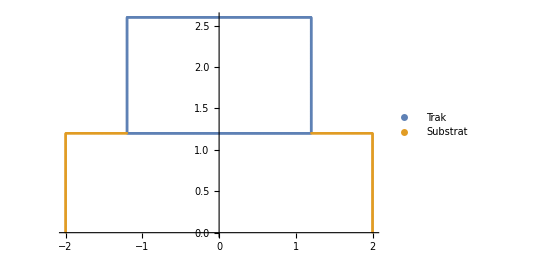

```mathematica
(* Podane vrednosti *)
sSubs = 2.0; (* Širina substrata *)
dSubs = 1.2; (* Debelina substrata *)
nSubsPrib = 1000; (* Približno število segmentov po celem pravokotnem objektu. To vrednost kasneje popravim na resnično število segmentov. *)
sTrak = 1.2;
dTrak = 1.4;
nTrakPrib = 1000;
ϵr= 10; (* Epsilon relativni za substrat*)
ϵ0 =8.854187812*10^(-12);

(* Generirane spremenljivke *)
hTrak ;(* Vektor Širine segmentov traka - prevodnika *)
nTrak; (* Število segmentov traka - prevodnika*)
hSubst;(* Isto, za substrat *)
nSubst;

(* Generiranje osnovnih točk in matrik*)
{tockeTrak,hTrak, nTrak}  = izracunajTockePravokotnika[sTrak, dTrak, nTrakPrib, dSubs, False, False,0];
{tockeSubst,hSubst, nSubst} = izracunajTockePravokotnika[sSubs,dSubs,nSubsPrib, 0, False, True,sTrak];
normaleTrak=vrniNormalneVektorjeSegmentov[tockeTrak];
normaleSubst=vrniNormalneVektorjeSegmentov[tockeSubst];

(*Risanje*)
normaleTrakRisanje=vrniNormalneVektorjeSegmentovVTočki[tockeTrak];
normaleSubstRisanje=vrniNormalneVektorjeSegmentovVTočki[tockeSubst];
ListPlot[{tockeTrak, tockeSubst},PlotLegends->{"Trak","Substrat"}, AspectRatio->Automatic]
drawNormTrak=Table[Arrow[normaleTrak[[i]]], {i,1,Length[normaleTrak]}];
drawNormSubst=Table[Arrow[normaleSubst[[i]]], {i, 1, Length[normaleSubst]}];
Graphics[{drawNormTrak, drawNormSubst}];
```

```mathematica
(*Računanje nabojev*)
b = vrniVektorB[12, Length[tockeTrak], Length[tockeSubst]];
A= vrniMatrikoA[tockeTrak, tockeSubst, hTrak, hSubst, normaleTrak, normaleSubst, ϵr];
q=LinearSolve[A,b];
```

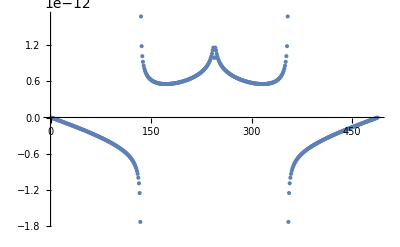

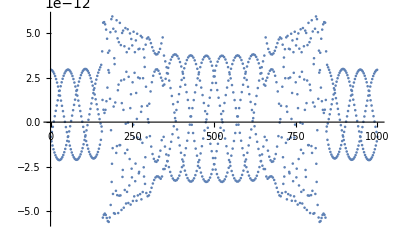

-Graphics3D-

```mathematica
(*Risanje*)
qTrak=q[[1;;nTrak]];
qSubst = q[[nTrak+1;;nTrak+nSubst]];
ListPlot[qSubst]
ListPlot[qTrak]

qTrak[[i]];
rTrak=Table[{tockeTrak[[i]][[1]], tockeTrak[[i]][[2]],qTrak[[i]]}, {i, 1, nTrak}];
rSubst=Table[{tockeSubst[[i]][[1]], tockeSubst[[i]][[2]],qSubst[[i]]}, {i, 1, nSubst}];
ListPointPlot3D[{rTrak, rSubst},  AspectRatio->Automatic, PlotRange->{{-3.3,3.3},{0,3.7}}, Filling->Axis]
```